```mathematica
Module[{α=0.01,β=0.01},
αn=Table[{n,4^n α},{n,0,6}];
βn=Table[{n,2^(n^2+n)α^(n-1)β(2^n α+α+β)},{n,0,6}];]
```

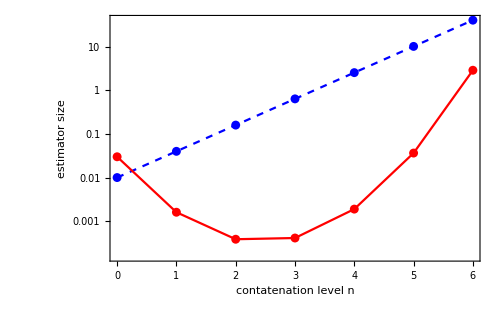

```mathematica
pic=ListLogPlot[{αn,βn},Joined->True,Mesh->All,Frame->True,ImageSize->500,FrameLabel->{"contatenation level n",},FrameStyle->Directive[16,"Times"],PlotLegends->MaTeX[{"\\alpha_{(n)}","\\beta_{(n)}"},FontSize->20],PlotStyle->{Directive[Blue,Dashed],Directive[Red]}]
```

```mathematica
NotebookDirectory[]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/

```mathematica
Export[NotebookDirectory[]<>"../img/alpha-beta-estimator.pdf",pic]
```

/Users/jiaan/Desktop/DD-threshold/notebooks/../img/alpha-beta-estimator.pdf